```mathematica
SetDirectory[NotebookDirectory[]];
```

# h_scaling

## data

```mathematica
(*mpi=Flatten[Import["./pionmass/LPA_hscaling_mub0/buffer/mPion.dat"]];*)
```

```mathematica
fpi=Flatten[Import["./mub0/buffer/fpi.dat"]];
h=Flatten[Import["./mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub0=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
(*h1mub0linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];*)
fpi=Flatten[Import["./mub300/buffer/fpi.dat"]];
h=Flatten[Import["./mub300/buffer/c.dat"]]*197.33^3;
datamub300=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub300=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
(*h1mub300linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];*)
fpi=Flatten[Import["./mub400/buffer/fpi.dat"]];
h=Flatten[Import["./mub400/buffer/c.dat"]]*197.33^3;
datamub400=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub400=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
(*h1mub400linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];*)
fpi=Flatten[Import["./mub500/buffer/fpi.dat"]];
h=Flatten[Import["./mub500/buffer/c.dat"]]*197.33^3;
datamub500=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub500=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
(*h1mub500linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];*)
fpi=Flatten[Import["./mub600/buffer/fpi.dat"]];
h=Flatten[Import["./mub600/buffer/c.dat"]]*197.33^3;
datamub600=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub600=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
(*h1mub600linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];*)
fpi=Flatten[Import["./mub620/buffer/fpi.dat"]];
h=Flatten[Import["./mub620/buffer/c.dat"]]*197.33^3;
datamub620=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub620=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub620[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
(*h1mub620linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub620[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];*)
```

## Plot

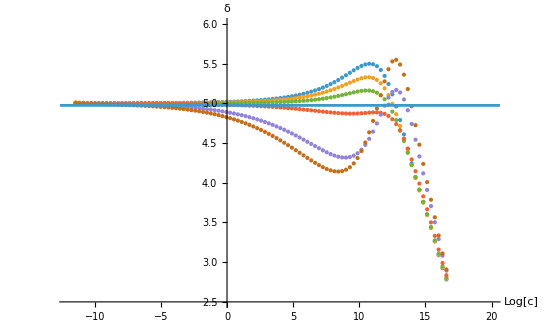

```mathematica
ploth=Show[ListPlot[{h1mub0,h1mub300,h1mub400,h1mub500,h1mub600,h1mub620},AxesLabel->{"Log[c]","δ"},PlotLegends->{(*"μ_B=0","μ_B=50MeV","μ_B=100MeV","μ_B=150MeV","μ_B=200MeV","μ_B=250MeV","μ_B=300MeV","μ_B=350MeV",*)(*"μ_B=400MeV","μ_B=450MeV","μ_B=500MeV","μ_B=550MeV"*)(*,"μ_B=600MeV","μ_B=650MeV","μ_B=700MeV"*)},Axes->True,PlotRange->{{-12,20},{2.5,6}}],ListLinePlot[{{-20,4.975},{100,4.975}}]]
```

```mathematica
(*Export["./LPA_Tscaling_hot/mub0.dat",h1mub0linear];
Export["./LPA_Tscaling_hot/mub50.dat",h1mub50linear];
Export["./LPA_Tscaling_hot/mub100.dat",h1mub100linear];
Export["./LPA_Tscaling_hot/mub150.dat",h1mub150linear];
Export["./LPA_Tscaling_hot/mub200.dat",h1mub200linear];
Export["./LPA_Tscaling_hot/mub250.dat",h1mub250linear];
Export["./LPA_Tscaling_hot/mub300.dat",h1mub300linear];
Export["./LPA_Tscaling_hot/mub350.dat",h1mub350linear];
Export["./LPA_Tscaling_hot/mub400.dat",h1mub400linear];
Export["./LPA_Tscaling_hot/mub450.dat",h1mub450linear];
Export["./LPA_Tscaling_hot/mub500.dat",h1mub500linear];
Export["./LPA_Tscaling_hot/mub550.dat",h1mub550linear];
Export["./LPA_Tscaling_hot/mub600.dat",h1mub600linear];
Export["./LPA_Tscaling_hot/mub650.dat",h1mub650linear];
Export["./LPA_Tscaling_hot/mub700.dat",h1mub700linear];*)
```